# NNPDF Mathematica package example code (helicity-averaged PDFs)

## PRELIMINARY TASKS

Clear all definitions.

```mathematica
Clear["Global`*"];
```

Change the pdfpath to the location where the NNPDF.m file is stored.

```mathematica
pdfpath=NotebookDirectory[];
SetDirectory[pdfpath];
```

Load the Mathematica package containing global variables and functions to access NNPDF Set grids.

```mathematica
<<NNPDF`
```

Welcome in the Mathematica Package for NNPDF PDFs. The following Functions are available:

- Initializing and interpolating PDFs

InitializePDFGrid;

- Using NNPDF PDFs

xPDFcv; xPDFEnsemble; xPDFRep; xPDF; xPDFCL; xMin; xMax; Q2min; Q2Max; NumberPDF; HasPhoton;

- Parameters for the QCD analysis

alphaSMZ; mCharm; mBottom; mTop; MZ; alphas; Infoalphas; Lam4; Lam5;

For the usage of each of these Functions, please read the README file or type ?Function.

Look at the functions implemented in the NNPDF package.

```mathematica
?InitializePDFGrid
```

```mathematica
?xPDFcv
```

The function xPDFcv[x, QSq, f] returns x times the central value of the PDF with flavor f at a given momentum fraction x and scale QSq in Gev^2. Note that f must be an integer, and x and QSq must be numeric quantities. For the unpolarized case, the LHAPDF convention is used for the flavor f , that is, f = -6, -5, -4, -3, -2, -1, 0, 1, 2, 3, 4, 5, 6 corresponds to tbar, bbar, cbar, sbar, ubar, dbar, g, d, u, s, c, b, t; f=7 returns the photon PDF (if available). Only for NNPDFpol1.0, the following convention is used for the flavor f, that is, f = 0, 1, 2, 3, 4 corresponds to polarized g, u+ubar, d+dbar, s+sbar.

```mathematica
?xPDFEnsemble
```

The function xPDFEnsemble[x, QSq, f] returns x times the vector of PDF replicas of flavor f at a given momentum fraction x and scale QSq in GeV^2. Note that f must be an integer, and x and QSq must be numeric quantities. For the unpolarized case, the LHAPDF convention is used for the flavor f, that is, f = -6, -5, -4, -3, -2, -1, 0, 1, 2, 3, 4, 5, 6 corresponds to tbar, bbar, cbar, sbar, ubar, dbar, g, d, u, s, c, b, t; f=7 returns the photon PDF (if available). Only for NNPDFpol1.0, the following convention is used for the flavor f, that is, f = 0, 1, 2, 3, 4 corresponds to polarized g, u+ubar, d+dbar, s+sbar.

```mathematica
?xPDFRep
```

The function xPDFRep[x,QSq,f,irep] returns x times the irep PDF replica of flavor f at a given momentum fraction x and scale QSq in GeV^2. Note that f must be an integer, and x and QSq must be numeric quantities. For the unpolarized case, the LHAPDF convention is used for the flavor f, that is, f = -6, -5, -4, -3, -2, -1, 0, 1, 2, 3, 4, 5, 6 corresponds to tbar, bbar, cbar, sbar, ubar, dbar, g, d, u, s, c, b, t; f=7 returns the photon PDF (if available). Only for NNPDFpol1.0, the following convention is used for the flavor f, that is, f = 0, 1, 2, 3, 4 corresponds to polarized g, u+ubar, d+dbar, s+sbar.

```mathematica
?xPDF
```

The function xPDF[x,QSq,f] returns x times the value of the PDF of flavor f at a given momentum fraction x and scale QSq in GeV^2 with its standard deviation. Note that f must be an integer, and x and QSq must be numeric quantities. For the unpolarized case, the LHAPDF convention is used for the flavor f, that is, f = -6, -5, -4, -3, -2, -1, 0, 1, 2, 3, 4, 5, 6 corresponds to tbar, bbar, cbar, sbar, ubar, dbar, g, d, u, s, c, b, t; f=7 returns the photon PDF (if available). Only for NNPDFpol1.0, the following convention is used for the flavor f, that is, f = 0, 1, 2, 3, 4 corresponds to polarized g, u+ubar, d+dbar, s+sbar.

```mathematica
?xPDFCL
```

The function xPDFCL[ensemble,x,QSq,f,CL] returns x times the value of the PDF of flavor f at a given momentum fraction x and scale Q2 in GeV^2 with its error.  Note that f must be an integer, and x and QSq must be numeric quantities. For the unpolarized case, the LHAPDF convention is used for the flavor f, that is, f = -6, -5, -4, -3, -2, -1, 0, 1, 2, 3, 4, 5, 6 corresponds to tbar, bbar, cbar, sbar, ubar, dbar, g, d, u, s, c, b, t; f=7 returns the photon PDF (if available). Only for NNPDFpol1.0, the following convention is used for the flavor f, that is, f = 0, 1, 2, 3, 4 corresponds to polarized g, u+ubar, d+dbar, s+sbar. The variable ensemble is the PDF ensemble, as a function of x, QSq and f. It can be given by the function xPDFEnsemble (LHAPDF basis) or by any PDF ensemble (in a different basis) defined by the user. The variable CL denotes the confidence interval and must be a real number between 0 and 1.

```mathematica
?alphaSMZ
```

Returns the List of alphaS values at the Z mass used in the QCD analysis for each replica.

```mathematica
?mCharm
```

Charm quark mass in GeV.

```mathematica
?mBottom
```

Bottom quark masss in GeV.

```mathematica
?mTop
```

Top quark mass in GeV.

Set the path to the location of the grid files and the name of the grid you wish for usage. If you have installed the LHAPDF library, you should enter the path to the library. Notice that the name of the grid file must be entered without the .LHgrid suffix.

```mathematica
path="C:\\Users\\novar\\Dropbox\\NNPDF\\";
namegrid="NNPDF30_lo_as_0130";
```

Initialize and interpolate PDFs on the grid. Notice that this task must be performed only once at the beginning of your Mathematica session.

```mathematica
InitializePDFGrid[path,namegrid]
```

'Version' '5.8.8'

'Description:'

'NNPDF30_lo_as_0130.LHgrid'

'Reference: arXiv:1410.8849'

'Fit: LO global fit, alphas(MZ)=0.130'

'NNPDF Collaboration: R.D. Ball, V. Bertone, '

'S. Carrazza, C.S. Deans, L. Del Debbio, '

'S. Forte, A. Guffanti, N.P. Hartland, '

'J.I. Latorre, J. Rojo and M. Ubiali'

'This set has 100 member PDF'

'mem=0 --> average on replicas, positive definite'

'Evolution: pol. interpolation on the LH grid'

Grid division:

x axis: 100 points; 1.×10^-9 <= x <= 1.

Q^2 axis: 50 points; 1. <= Q^2 <= 1.×10^10

Reading PDF set from file. Please wait.

PDF set successfully read from file.

Interpolating PDF set on the grid. Please wait.

PDF grid interpolated. Ready to use the NNPDF set.

## USAGE OF THE PDF ENSEMBLE

### Central values and uncertainties

#### Central values

Fix the momentum fraction x and scale Q^2.

```mathematica
Clear[x,Q2];
x=0.4;
Q2=2.;
```

Fix the PDF flavor (all examples below refer to the gluon PDF, i.e. f=0).

```mathematica
Clear[f];
f=0;
```

You have two possibilities for getting the x*PDF central value. The first one is by using the buit-in function xPDFcv:

```mathematica
glu1=xPDFcv[x,Q2,f]
```

0.207023

The second one is by averaging over the x*PDF ensemble:

```mathematica
glu2=Mean[xPDFEnsemble[x,Q2,f]]
```

0.207023

Of course, you must obtain the same result.

#### Uncertainties

Uncertainties are given by the standard deviation computed over the x*PDF ensemble:

```mathematica
gluerr=StandardDeviation[xPDFEnsemble[x,Q2,f]]
```

0.0814585

You can also use the built-in function xPDF to get the mean value and the 1σ-uncertainty for the x*PDF quantity at the same time:

```mathematica
xPDF[x,Q2,f]
```

{0.207023,0.0814585}

#### Confidence intervals

There is also the possibility to get the mean value and the uncertainty at a given confidence level. First of all, set the confidence level (for example 68%)

```mathematica
Clear[CL];
CL=0.68;
```

Then, you can use the built-in function xPDFCL to get the mean value and the CL-uncertainty for the x*PDF quantity:

```mathematica
xPDFCL[xPDFEnsemble,x,Q2,f,CL]
```

{0.200253,0.0656897}

#### Single replicas

You may be interested in looking at a single x*PDF replica. Set the replica you want to sort out from the x*PDF ensemble:

```mathematica
rep=22;
```

Hence, you can use the built-in function xPDFRep to get the x*PDF value:

```mathematica
xPDFRep[x,Q2,0,rep]
```

0.196498

or specify the sorted replica from the function xPDFEnsemble, as follows:

```mathematica
xPDFEnsemble[x,Q2,0][[rep]]
```

0.196498

### Changing the PDF basis

First of all, clear the kinematic variables x and Q^2 and the PDF flavor.

```mathematica
Clear[x,Q2,f];
```

Any change of basis, from LHAPDF basis to any other convenient basis, is simply done by redefining each basis PDF from the PDF ensemble. In the following example the parametrization basis at the initial scale is used.

#### Parametrization basis {xΣ(x,Q_0^2), xg(x,Q_0^2), xs^+(x,Q_0^2), xT_3(x,Q_0^2), xV(x,Q_0^2), xΔ_S(x,Q_0^2), xs^-(x,Q_0^2)} at the initial scale Q_0^2=2 GeV^2.

```mathematica
xSinglet[x_,Q2_]:=(xPDFEnsemble[x,Q2,1]+xPDFEnsemble[x,Q2,-1])+(xPDFEnsemble[x,Q2,2]+xPDFEnsemble[x,Q2,-2])+(xPDFEnsemble[x,Q2,3]+xPDFEnsemble[x,Q2,-3]);
xGluon[x_,Q2_]:=xPDFEnsemble[x,Q2,0];
xStrangeness[x_,Q2_]:=xPDFEnsemble[x,Q2,3]+xPDFEnsemble[x,Q2,-3];
xTriplet[x_,Q2_]:=(xPDFEnsemble[x,Q2,2]+xPDFEnsemble[x,Q2,-2])-(xPDFEnsemble[x,Q2,1]+xPDFEnsemble[x,Q2,-1]);
xValence[x_,Q2_]:=(xPDFEnsemble[x,Q2,1]-xPDFEnsemble[x,Q2,-1])+(xPDFEnsemble[x,Q2,2]-xPDFEnsemble[x,Q2,-2])+(xPDFEnsemble[x,Q2,3]-xPDFEnsemble[x,Q2,-3]);
xSeaAsy[x_,Q2_]:=xPDFEnsemble[x,Q2,-1]-xPDFEnsemble[x,Q2,-2];
xStrangeAsy[x_,Q2_]:=xPDFEnsemble[x,Q2,3]-xPDFEnsemble[x,Q2,-3];
```

```mathematica
xPDFParametrization[x_,Q2_,f_]:=Which[f==1,xSinglet[x,Q2],f==2,xGluon[x,Q2],f==3,xStrangeness[x,Q2],f==4,xTriplet[x,Q2],f==5,xValence[x,Q2],f==6,xSeaAsy[x,Q2],f==7,xStrangeAsy[x,Q2]];
```

### Plotting the PDFs in a given basis

Clear the kinematic variables.

```mathematica
Clear[x,Q2,f];
```

Set the parametrization basis.

```mathematica
mvxParametrization[x_,Q2_,f_]:=Mean[xPDFParametrization[x,Q2,f]];
sdxParametrization[x_,Q2_,f_]:=StandardDeviation[xPDFParametrization[x,Q2,f]];
```

#### Linear scale

Define a suitable function for plotting PDFs in linear scale.

```mathematica
PlotxPDFlin[f_,xmin_,xmax_,ymin_,ymax_,Q2_]:=Plot[{mvxParametrization[x,Q2,f]+sdxParametrization[x,Q2,f],mvxParametrization[x,Q2,f]-sdxParametrization[x,Q2,f]},{x,xmin,xmax},Filling->{1->{{2},Green}},PlotRange->{Automatic,{ymin,ymax}},ImageSize->500];
```

xΣ(x,Q_0^2)

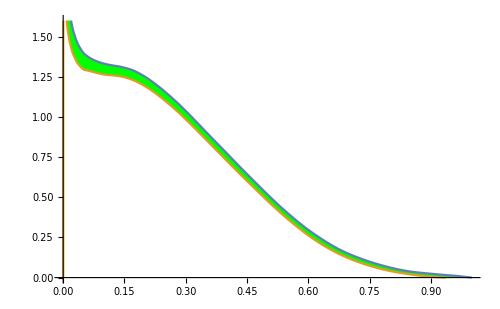

```mathematica
Clear[f,xmin,xmax,ymin,ymax,Q20];
f=1;
xmin=0.;
xmax=1.;
ymin=0.;
ymax=1.6;
Q20=2.;
PlotxPDFlin[f,xmin,xmax,ymin,ymax,Q20]
```

xg(x,Q_0^2)

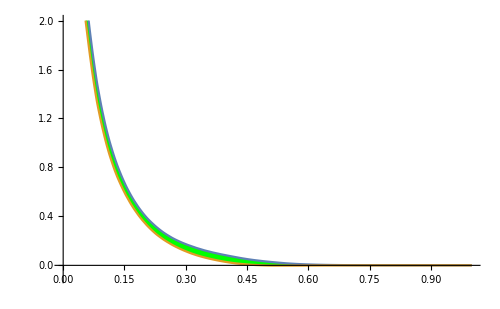

```mathematica
Clear[f,xmin,xmax,ymin,ymax,Q20];
f=2;
xmin=0.;
xmax=1.;
ymin=-0.1;
ymax=2;
Q20=10^2.;
PlotxPDFlin[f,xmin,xmax,ymin,ymax,Q20]
```

xs^+(x,Q_0^2)

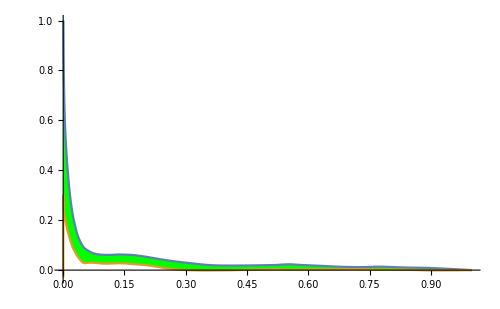

```mathematica
Clear[f,xmin,xmax,ymin,ymax,Q20];
f=3;
xmin=0.;
xmax=1.;
ymin=-.03;
ymax=1.;
Q20=2.;
PlotxPDFlin[f,xmin,xmax,ymin,ymax,Q20]
```

xT_3(x,Q_0^2)

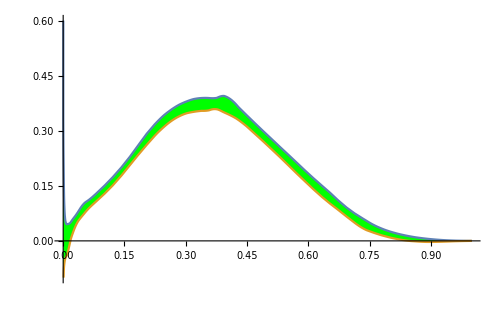

```mathematica
Clear[f,xmin,xmax,ymin,ymax,Q20];
f=4;
xmin=0.;
xmax=1.;
ymin=-.1;
ymax=.6;
Q20=2.;
PlotxPDFlin[f,xmin,xmax,ymin,ymax,Q20]
```

xV(x,Q_0^2)

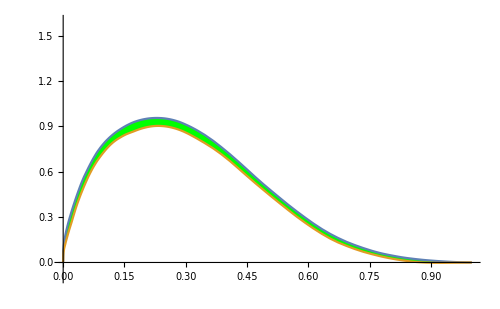

```mathematica
Clear[f,xmin,xmax,ymin,ymax,Q20];
f=5;
xmin=0.;
xmax=1.;
ymin=-.1;
ymax=1.6;
Q20=2.;
PlotxPDFlin[f,xmin,xmax,ymin,ymax,Q20]
```

xΔ_S(x,Q_0^2)

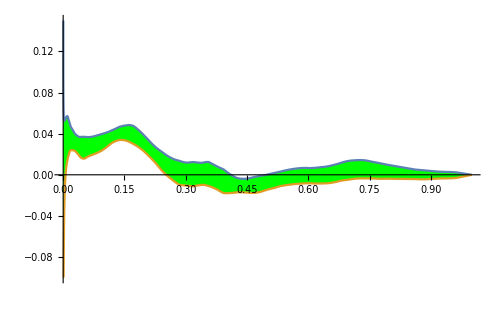

```mathematica
Clear[f,xmin,xmax,ymin,ymax,Q20];
f=6;
xmin=0.;
xmax=1.;
ymin=-.1;
ymax=.15;
Q20=2.;
PlotxPDFlin[f,xmin,xmax,ymin,ymax,Q20]
```

xs^-(x,Q_0^2)

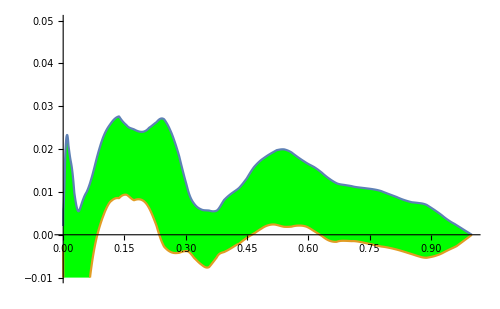

```mathematica
Clear[f,xmin,xmax,ymin,ymax,Q20];
f=7;
xmin=0.;
xmax=1.;
ymin=-.01;
ymax=.05;
Q20=2.;
PlotxPDFlin[f,xmin,xmax,ymin,ymax,Q20]
```

#### Logarithmic scale

Define a suitable function for plotting PDFs in logarithmic scale.

```mathematica
PlotxPDFlog[f_,xmin_,xmax_,ymin_,ymax_,Q2_]:=Plot[{mvxParametrization[10^x,Q2,f]+sdxParametrization[10^x,Q2,f],mvxParametrization[10^x,Q2,f]-sdxParametrization[10^x,Q2,f]},{x,xmin,xmax},Filling->{1->{{2},Green}},PlotRange->{Automatic,{ymin,ymax}},ImageSize->500,AxesOrigin->{xmin,ymin},Ticks->{Flatten[Table[Table[{l+1-1/9*(10^(0.1*i)-1),If[FractionalPart[l+1-1/9*(10^(0.1*i)-1)]==0,ScientificForm[10^(l+1),0,NumberMultiplier->" "]," "]},{i,0,9}],{l,xmin,xmax-1}],1],Automatic}];
```

xΣ(x,Q_0^2)

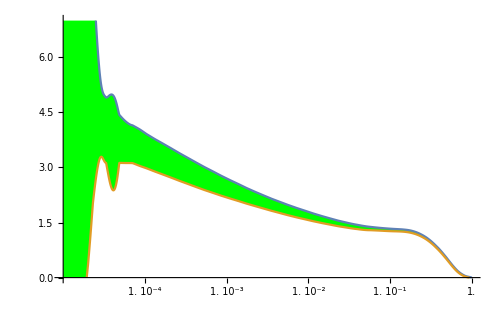

```mathematica
Clear[f,xmin,xmax,ymin,ymax,Q20];
f=1;
xmin=-5.;
xmax=0.;
ymin=0.;
ymax=7.;
Q20=2.;
PlotxPDFlog[f,xmin,xmax,ymin,ymax,Q20]
```

xg(x,Q_0^2)

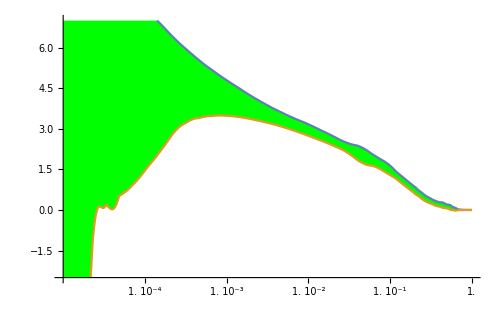

```mathematica
Clear[f,xmin,xmax,ymin,ymax,Q20];
f=2;
xmin=-5.;
xmax=0.;
ymin=-2.5;
ymax=7.;
Q20=2.;
PlotxPDFlog[f,xmin,xmax,ymin,ymax,Q20]
```

xs^+(x,Q_0^2)

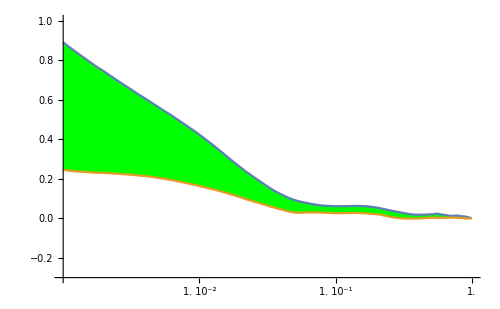

```mathematica
Clear[f,xmin,xmax,ymin,ymax,Q20];
f=3;
xmin=-3.;
xmax=0.;
ymin=-.3;
ymax=1.;
Q20=2.;
PlotxPDFlog[f,xmin,xmax,ymin,ymax,Q20]
```

### Further plots

#### Single replicas

You may be interested in comparing the plot of single replicas with the mean value and error band for a specified PDF. The followng example refers to the Singlet PDF (f=1 in the parametrization basis) plotted in logarithmic scale. You should have runned the functions defined in subsec. “Changing the PDF basis”.

Clear the kinematic variables.

```mathematica
Clear[x,Q2,f];
```

Set the parametrization basis.

```mathematica
mvxParametrization[x_,Q2_,f_]:=Mean[xPDFParametrization[x,Q2,f]];
sdxParametrization[x_,Q2_,f_]:=StandardDeviation[xPDFParametrization[x,Q2,f]];
```

Define a suitable function for plotting PDFs in logarithmic scale.

```mathematica
PlotxPDFlog[f_,xmin_,xmax_,ymin_,ymax_,Q2_,num_]:=
ListLogLinearPlot[{Table[{xmin*(xmax/xmin)^(i/num),mvxParametrization[xmin*(xmax/xmin)^(i/num),Q2,f]+sdxParametrization[xmin*(xmax/xmin)^(i/num),Q2,f]},{i,0,num}],Table[{xmin*(xmax/xmin)^(i/num),mvxParametrization[xmin*(xmax/xmin)^(i/num),Q2,f]-sdxParametrization[xmin*(xmax/xmin)^(i/num),Q2,f]},{i,0,num}]},ImageSize->500,Joined->True,Filling->{1->{{2},Green}},PlotRange->{Automatic,{ymin,ymax}}];
```

Define a suitable function for plotting PDF replicas in logarithmic scale.

```mathematica
PlotxPDFreplog[f_,xmin_,xmax_,ymin_,ymax_,Q2_,replicas_,num_]:=ListLogLinearPlot[Table[Table[{xmin*(xmax/xmin)^(i/num),xPDFParametrization[xmin*(xmax/xmin)^(i/num),Q2,f][[j]]},{i,0,num}],{j,1,replicas}],ImageSize->500,Joined->True,PlotRange->{Automatic,{ymin,ymax}}];
```

Define the variables appearing in these functions.

```mathematica
Clear[f,xmin,xmax,ymin,ymax,Q20,replicas];
f=1;
xmin=10^(-5);
xmax=1;
ymin=0.;
ymax=7.;
Q20=2.;
num=100;
replicas=30;
```

Make the plots:

```mathematica
plot1=PlotxPDFlog[f,xmin,xmax,ymin,ymax,Q20,num];
```

```mathematica
plot2=PlotxPDFreplog[f,xmin,xmax,ymin,ymax,Q20,replicas,num];
```

Show the plots:

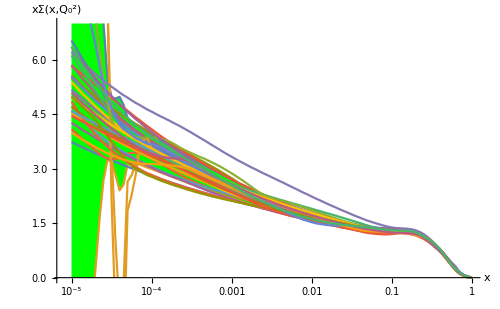

```mathematica
plotrep=Show[{plot1,plot2},AxesLabel->{"x","xΣ(x,Q_0^2)"},ImageSize->500]
```

#### Confidence intervals

You may be interested in comparing the plot of 1-σ with 68% CL error band for a specified PDF. The followng example refers to the Singlet PDF (f=1 in the parametrization basis) plotted in logarithmic scale. You should have runned the functions defined in subsec. “Changing the PDF basis”.

Clear the kinematic variables.

```mathematica
Clear[x,Q2,f];
```

Set the parametrization basis.

```mathematica
mvxParametrization[x_,Q2_,f_]:=Mean[xPDFParametrization[x,Q2,f]];
sdxParametrization[x_,Q2_,f_]:=StandardDeviation[xPDFParametrization[x,Q2,f]];
```

Define a suitable function for plotting 1-σ error band PDFs in logarithmic scale.

```mathematica
PlotxPDFlog[f_,xmin_,xmax_,ymin_,ymax_,Q2_,num_]:=
ListLogLinearPlot[{Table[{xmin*(xmax/xmin)^(i/num),mvxParametrization[xmin*(xmax/xmin)^(i/num),Q2,f]+sdxParametrization[xmin*(xmax/xmin)^(i/num),Q2,f]},{i,0,num}],Table[{xmin*(xmax/xmin)^(i/num),mvxParametrization[xmin*(xmax/xmin)^(i/num),Q2,f]-sdxParametrization[xmin*(xmax/xmin)^(i/num),Q2,f]},{i,0,num}]},ImageSize->500,Joined->True,Filling->{1->{{2},Green}},PlotRange->{Automatic,{ymin,ymax}}];
```

Define a suitable function for plotting 68% CL PDFs in logarithmic scale.

```mathematica
PlotxPDFCLlog[f_,xmin_,xmax_,ymin_,ymax_,Q2_,num_,CL_]:=ListLogLinearPlot[{Table[{xmin*(xmax/xmin)^(i/num),xPDFCL[xPDFParametrization,xmin*(xmax/xmin)^(i/num),Q2,f,CL][[1]]+xPDFCL[xPDFParametrization,xmin*(xmax/xmin)^(i/num),Q2,f,CL][[2]]},{i,0,num}],Table[{xmin*(xmax/xmin)^(i/num),xPDFCL[xPDFParametrization,xmin*(xmax/xmin)^(i/num),Q2,f,CL][[1]]-xPDFCL[xPDFParametrization,xmin*(xmax/xmin)^(i/num),Q2,f,CL][[2]]},{i,0,num}]},ImageSize->500,Joined->True,Filling->{1->{{2},Red}},PlotRange->{Automatic,{ymin,ymax}}];
```

Define the variables appearing in these functions.

```mathematica
Clear[f,xmin,xmax,ymin,ymax,Q20,CL];
f=1;
xmin=10^(-5);
xmax=1;
ymin=0.;
ymax=7.;
Q20=2.;
num=100;
CL=0.68;
```

Make the plots:

```mathematica
plot1=PlotxPDFlog[f,xmin,xmax,ymin,ymax,Q20,num];
```

```mathematica
plot2=PlotxPDFCLlog[f,xmin,xmax,ymin,ymax,Q20,num,CL];
```

Show the plots:

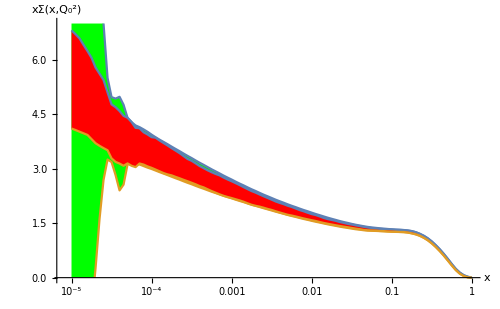

```mathematica
plotcl68=Show[{plot1,plot2},AxesLabel->{"x","xΣ(x,Q_0^2)"},ImageSize->500]
```

#### 3D and contour plots

Mathematica allows to draw a large variety of plots. In the following examples the Singlet PDF (f = 1 in the parametrization basis) 3D and contour plots are drawn in logarithmic scale. You should have runned the functions defined in subsec. "Changing the PDF basis".

```mathematica
f=1;
xmin=-5;
xmax=0;
Q2min=Log[10,2];
Q2minim=0;
Q2max=4;
min=0;
max=7;
plot1=Plot3D[{mvxParametrization[10^x,10^Q2,f]+sdxParametrization[10^x,10^Q2,f],mvxParametrization[10^x,10^Q2,f]-sdxParametrization[10^x,10^Q2,f]},{x,xmin,xmax},{Q2,Q2min,Q2max},Mesh->False,ClippingStyle->None,BoundaryStyle->Thick,PlotRange->{0,7},AxesLabel->{"x","Q^2","xΣ(x,Q^2)"},BoxRatios->{1.5,1.3,1},ImageSize->500,Axes->{True,True,True},BoxStyle->Directive[Dashed],AxesStyle->{Thickness[0.003],Thickness[0.003],Thickness[0.003]},Ticks->{Flatten[Table[Table[{l+1-1/9*(10^(0.1*i)-1),If[FractionalPart[l+1-1/9*(10^(0.1*i)-1)]==0,N[10^(l+1)]," "]},{i,0,9}],{l,xmin,xmax-1}],1],Flatten[Table[Table[{l+1-1/9*(10^(0.1*i)-1),If[FractionalPart[l+1-1/9*(10^(0.1*i)-1)]==0,ScientificForm[10^(l+1),0,NumberMultiplier->" "]," "]},{i,0,9}],{l,Q2minim,Q2max-1}],1],Automatic}]
```

-Graphics3D-

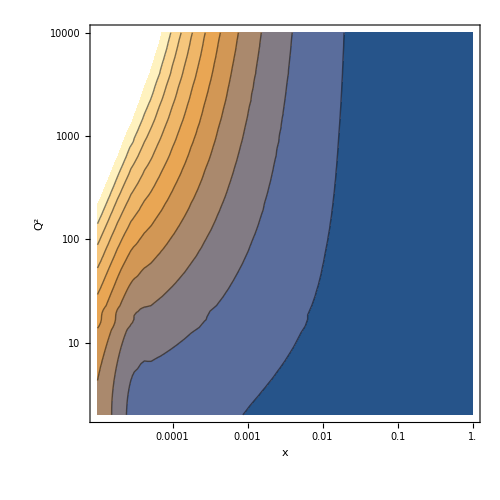

```mathematica
plot2=ContourPlot[mvxParametrization[10^x,10^Q2,f],{x,xmin,xmax},{Q2,Q2min,Q2max},FrameLabel->{"x","Q^2"},FrameTicks->{{Flatten[Table[Table[{l+1-1/9*(10^(0.1*i)-1),If[FractionalPart[l+1-1/9*(10^(0.1*i)-1)]==0,ScientificForm[10^(l+1),0,NumberMultiplier->" "]," "]},{i,0,9}],{l,Q2minim,Q2max-1}],1],None},{Flatten[Table[Table[{l+1-1/9*(10^(0.1*i)-1),If[FractionalPart[l+1-1/9*(10^(0.1*i)-1)]==0,N[10^(l+1)]," "]},{i,0,9}],{l,xmin,xmax-1}],1],None}},ImageSize->500]
```

### Checking momentum sum rules

In the following example, momentum sum rules are checked. This example is intended to show how any physical observable depending on PDFs can be computed. You should have runned the functions defined in subsec. “Changing the PDF basis”.

```mathematica
Clear[Q20,replicas,integral];
Q20=2;
replicas=100;
```

### Momentum sum rule

```mathematica
integral=Table[NIntegrate[(xSinglet[x,Q20][[j]]+xGluon[x,Q20][[j]]),{x,10^(-9),1}],{j,1,replicas}];
{Mean[integral],StandardDeviation[integral]}
```

{1.03002,0.0269733}

We obtain  ∫_(10^-9)^1 x[Σ(x)Σ+g(x)]ⅆx=1.00061±0.00140, in agreement with ∫_0^1 x[Σ(x)Σ+g(x)]ⅆx=1.

### Valence sum rules

```mathematica
integral=Table[NIntegrate[(xPDFEnsemble[x,Q20,2][[j]]/x-xPDFEnsemble[x,Q20,-2][[j]]/x),{x,10^(-9),1}],{j,1,replicas}];
N[{Mean[integral],StandardDeviation[integral]},5]
```

{1.99579,0.00716833}

We obtain ∫_(10^-9)^1 [u(x)-ū(x)]ⅆx=2.002±0.017, in agreement with ∫_0^1 [u(x)-ū(x)]ⅆx=2.

```mathematica
integral=Table[NIntegrate[(xPDFEnsemble[x,Q20,1][[j]]/x-xPDFEnsemble[x,Q20,-1][[j]]/x),{x,10^(-9),1}],{j,1,replicas}];
{Mean[integral],StandardDeviation[integral]}
```

{0.99186,0.0074392}

We obtain ∫_(10^-9)^1 [d(x)-d̄(x)]ⅆx=0.99999±0.01251, in agreement with  ∫_0^1 [d(x)-d̄(x)]ⅆx=1.